```mathematica
A=170;
deltaE[delta_,n_,l_,j_,k_]:=-2/3*41*A^(-1/3)(n+3/2)*delta*((3 k^2-j(j+1))(3/4-j(j+1)))/((2j-1)j(j+1)(2j+1));
(* Example for i(13/2) orbit *)
Kratio=0.57;
N0=5;
delta0=0.22;
l=6;
lm1=5;
j=6.5;
j2=4.5;
deltaTablej132=Table[{x,deltaE[delta0,N0,l,j,x]},{x,0.5,j,1}];
deltaTablej92=Table[{x,deltaE[delta0,N0,lm1,j2,x]},{x,0.5,j2,1}];
deltaTablej132
deltaTablej92
```

{{0.5,-1.98493},{1.5,-1.73681},{2.5,-1.24058},{3.5,-0.496231},{4.5,0.496231},{5.5,1.73681},{6.5,3.2255}}

{{0.5,-2.05259},{1.5,-1.53945},{2.5,-0.513148},{3.5,1.0263},{4.5,3.07889}}

```mathematica
p=ListPlot[{deltaTablej132,deltaTablej92},ImageSize->Medium,Joined->True,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"K","ΔE"},LabelStyle->{21,Bold,Black,FontFamily->"Times"},FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,Automatic},{Table[k,{k,1/2,13/2,1}],Automatic}},PlotRange->{Full,{-2.8,3.4}},PlotLegends->Placed[{"i_(13/2)","h_(9/2)"},{0.8,0.25}]];
```

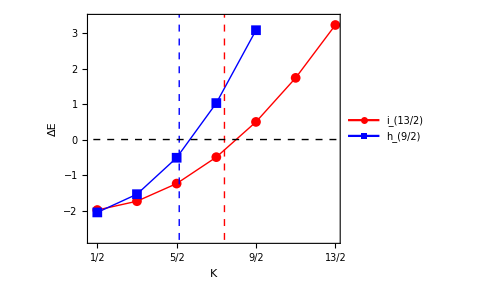

```mathematica
gfx=Show[{p,Graphics[{Blue,Dashed,Line[{{Kratio*j2,-4},{Kratio*j2,4}}]}],Graphics[{Dashed,Red,Line[{{Kratio*j,-4},{Kratio*j,4}}]}],Graphics[{Dashed,Black,Thick,Line[{{-1,0},{8,0}}]}]}];
Show[gfx]
```

```mathematica
m1miniPath="/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/nilsson-energy-shift/";
Export[StringTemplate["``energy_shift_nilssonDeltaE.pdf"][m1miniPath],Show[gfx], ImageResolution->1200];
```